Influence of the closing angle on the current peak in a simple R-L circuit

Definition of a circuit parameters

```mathematica
R = 5
L = 0.1
XL = 2*Pi*f*L
fi = ArcTan[XL/R]
Cos[fi]
```

5

0.1

31.4159

1.41297

0.157177

```mathematica
f = 50
```

50

Closing angle

```mathematica
alpha = 0
```

0

Voltage definition

```mathematica
U = 230
u[t_, alfa_] = Sqrt[2]*U*Sin[2*Pi*f*t+alfa]
```

230

230 √2 Sin[alfa+100 π t]

Current function definition

```mathematica
i[t_, alfa_]=Sqrt[2]*U/Sqrt[R^2+XL^2]*{Sin[2*Pi*f*t+alfa-fi]-Sin[alfa-fi]*Exp[-R/L*t]}
```

{10.2249 (ⅇ^(-50. t) Sin[1.41297-alfa]-Sin[1.41297-alfa-100 π t])}

```mathematica
iu[t_, alfa_] = Sqrt[2]*U/Sqrt[R^2+XL^2]*Sin[2*Pi*f*t+alfa-fi]
```

-10.2249 Sin[1.41297-alfa-100 π t]

```mathematica
idc[t_, alfa_] = Sqrt[2]*U/Sqrt[R^2+XL^2]*{-Sin[alfa-fi]*Exp[-R/L*t]}
```

{10.2249 ⅇ^(-50. t) Sin[1.41297-alfa]}

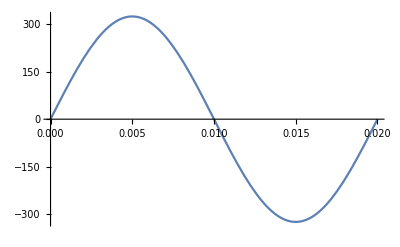

```mathematica
Plot[u[t, alpha], {t, 0, 0.02}, PlotLegends -> "Expressions"]
```

Time constant

```mathematica
L/R
```

0.02

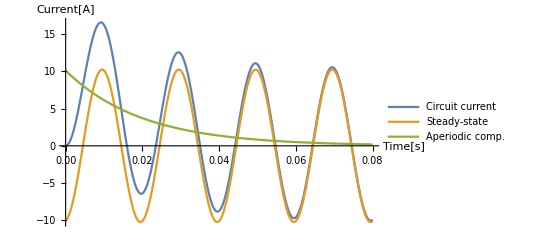

```mathematica
Plot[{i[t, alpha], iu[t, alpha],idc[t, alpha]}, {t, 0, 0.08},  AxesLabel -> {"Time[s]", "Current[A]"}, PlotLegends -> {"Circuit current", "Steady-state", "Aperiodic comp."}]
```

```mathematica
Manipulate[Plot[{i[t, a], iu[t, a],idc[t, a]}, {t, 0, 0.08}, AxesLabel -> {"Time[s]", "Current[A]"}], {a, 0, fi}]
```